```mathematica
Exit
```

Load the packages (Teukolsky must by imported first)

```mathematica
<<Teukolsky`
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["SpinningTrajectory.wl"]
Get["TeukolskySpinFluxes.wl"]
```

## Trajectory

Orbital parameters

```mathematica
a=0.95`48
p=10.0`48
e=0.2`48
x=0.8`48
```

0.95

10.

0.2

0.8

Numerically calculated correction to the orbit

```mathematica
orbitCorrGenNum=KerrSpinOrbitCorrection[a, p, e, x, 8, 8]
```

Calculating t, ϕ equations

Calculating r equation

Calculating θ equation

Calculating norm equation

Calculating submatrices

Calculating v

Calculating ES,LS

Calculating UtSlist, UϕSlist

Calculating Uthatlist, Uϕhatlist

Calculating UtSfour, UϕSfour

Calculating Uthatfour, Uϕhatfour

Calculating ImΔtSfour, ImΔϕSfour

<|a→0.95,p→10.,e→0.2,ℐ→0.64350110879328438680280922871732263804151059112,Ehat→0.9544746770348815028245737919294451657838972805,Lzhat→2.79948425680011891564236595392544962217500193,Khat→8.0197239367489946559142268066245112912793203,TrajectoryCorrection→{Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`ΔtS$32282[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`rS$32282[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`zS$32282[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`ΔϕS$32282[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]]},TrajectoryGeo→{Function[{qt$,qr$,qθ$},qt$+37.66072847086401572836785676378822407973456 (0.999413390411955398085512051676789953825169 (π/2+qθ$)-EllipticE[JacobiAmplitude[1.0005871263100361282233286778813341185737146 (π/2+qθ$),0.0023454059187486273529280769211641734494410904],0.0023454059187486273529280769211641734494410904])-0.33817361288513973186269357261612270765611991 (-44.948693400468249365643857431842061032604956 (-8.715797818536671656955276473503844727558 (0.5059439843226725349628859729866393707486 qr$-EllipticPi[0.0001841712845929680574511269209054036693793,JacobiAmplitude[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563],0.04594999780221134188374541608125003015055563])+0.2020991546530951596132878618750486375788946 (0.5138663607127461504485150319017451954413448 qr$-EllipticPi[0.03059916228279354923394371188192864618810053,JacobiAmplitude[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563],0.04594999780221134188374541608125003015055563]))+185.8084378216365257371440228116034607695374 (0.639534709428175376839293227058901935148601 qr$-EllipticPi[0.3725467329299748343441276990258976572072919,JacobiAmplitude[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563],0.04594999780221134188374541608125003015055563])+89.529529757449739111338408326286046756355518 (0.4942057923127259889166562805682094528702252 qr$-EllipticE[JacobiAmplitude[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563],0.04594999780221134188374541608125003015055563]+(0.3725467329299748343441276990258976572072919 JacobiCN[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563] JacobiSN[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563] √(1-0.04594999780221134188374541608125003015055563 JacobiSN[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563]^2))/(1-0.3725467329299748343441276990258976572072919 JacobiSN[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563]^2))),Listable],Function[{qr$},(-93.202326454836286463247075469243991457090653+5.482170105915190101709795598711337604788007 JacobiSN[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563]^2)/(-11.184279174580354375589649056309278974850878+4.1666666666666666666666666666666666666666666667 JacobiSN[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563]^2),Listable],Function[{qθ$},ArcCos[0.6 JacobiSN[1.0005871263100361282233286778813341185737146 (π/2+qθ$),0.0023454059187486273529280769211641734494410904]],Listable],Function[{qϕ$,qr$,qθ$},qϕ$+1.0288712096409793695217593013980787298979828 (-46.61009445803144762574408165284621114352 (0.5059439843226725349628859729866393707486 qr$-EllipticPi[0.0001841712845929680574511269209054036693793,JacobiAmplitude[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563],0.04594999780221134188374541608125003015055563])+2.062164084552230624278761438206890087165815 (0.5138663607127461504485150319017451954413448 qr$-EllipticPi[0.03059916228279354923394371188192864618810053,JacobiAmplitude[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563],0.04594999780221134188374541608125003015055563]))-0.79738973499649480880213907443707012421368236 (1.2508154931005795747794382586319016068093013 (π/2+qθ$)-EllipticPi[0.36,JacobiAmplitude[1.0005871263100361282233286778813341185737146 (π/2+qθ$),0.0023454059187486273529280769211641734494410904],0.0023454059187486273529280769211641734494410904]),Listable]},MinoFrequenciesGeo→{124.7629736005981287023759422670878097996,2.78953935181040098671000383825122170656255,3.5087504235493092486810623834629999915272225,3.69314850594018026158987829353258678045},BLFrequenciesGeo→{0.02235871165383178715389082048398869326539,0.02812333116379399823078257715580813748831,0.0296013183988624880244706636949406850169},FourVelocityCorrection→{Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`udtS$32282[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},(10. 0.2 (SpinningOrbit`Private`χrhat$32282'[SpinningOrbit`Private`wr$] (Cos[SpinningOrbit`Private`χrhat$32282[SpinningOrbit`Private`wr$]] SpinningOrbit`Private`δχrS$32282[SpinningOrbit`Private`wr$] SpinningOrbit`Private`Υrhat$32282+Sin[SpinningOrbit`Private`χrhat$32282[SpinningOrbit`Private`wr$]] SpinningOrbit`Private`ΥrS$32282+(2 0.2 Sin[SpinningOrbit`Private`χrhat$32282[SpinningOrbit`Private`wr$]]^2 SpinningOrbit`Private`δχrS$32282[SpinningOrbit`Private`wr$] SpinningOrbit`Private`Υrhat$32282)/(1+0.2 Cos[SpinningOrbit`Private`χrhat$32282[SpinningOrbit`Private`wr$]]))+Sin[SpinningOrbit`Private`χrhat$32282[SpinningOrbit`Private`wr$]] SpinningOrbit`Private`dδχrS$32282[SpinningOrbit`Private`wr$]))/(1+0.2 Cos[SpinningOrbit`Private`χrhat$32282[SpinningOrbit`Private`wr$]])^2+SpinningOrbit`Private`dδ𝔯$32282[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},-Sin[SpinningOrbit`Private`ℐ$32282] (SpinningOrbit`Private`χθhat$32282'[SpinningOrbit`Private`wz$] (Cos[SpinningOrbit`Private`χθhat$32282[SpinningOrbit`Private`wz$]] SpinningOrbit`Private`δχθS$32282[SpinningOrbit`Private`wz$] SpinningOrbit`Private`Υθhat$32282+Sin[SpinningOrbit`Private`χθhat$32282[SpinningOrbit`Private`wz$]] SpinningOrbit`Private`ΥθS$32282)+Sin[SpinningOrbit`Private`χθhat$32282[SpinningOrbit`Private`wz$]] SpinningOrbit`Private`dδχθS$32282[SpinningOrbit`Private`wz$])+SpinningOrbit`Private`dδ𝔷$32282[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`udϕS$32282[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]]},Spin4vector→{Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`St$32282[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`Sr$32282[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`Sz$32282[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`Sϕ$32282[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]]},TrajectoryDeltas→<|Δtr→Function[{qr$},-0.33817361288513973186269357261612270765611991 (-44.948693400468249365643857431842061032604956 (-8.715797818536671656955276473503844727558 (0.5059439843226725349628859729866393707486 qr$-EllipticPi[0.0001841712845929680574511269209054036693793,JacobiAmplitude[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563],0.04594999780221134188374541608125003015055563])+0.2020991546530951596132878618750486375788946 (0.5138663607127461504485150319017451954413448 qr$-EllipticPi[0.03059916228279354923394371188192864618810053,JacobiAmplitude[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563],0.04594999780221134188374541608125003015055563]))+185.8084378216365257371440228116034607695374 (0.639534709428175376839293227058901935148601 qr$-EllipticPi[0.3725467329299748343441276990258976572072919,JacobiAmplitude[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563],0.04594999780221134188374541608125003015055563])+89.529529757449739111338408326286046756355518 (0.4942057923127259889166562805682094528702252 qr$-EllipticE[JacobiAmplitude[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563],0.04594999780221134188374541608125003015055563]+(0.3725467329299748343441276990258976572072919 JacobiCN[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563] JacobiSN[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563] √(1-0.04594999780221134188374541608125003015055563 JacobiSN[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563]^2))/(1-0.3725467329299748343441276990258976572072919 JacobiSN[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563]^2))),Listable],Δtθ→Function[{qθ$},37.66072847086401572836785676378822407973456 (0.999413390411955398085512051676789953825169 (π/2+qθ$)-EllipticE[JacobiAmplitude[1.0005871263100361282233286778813341185737146 (π/2+qθ$),0.0023454059187486273529280769211641734494410904],0.0023454059187486273529280769211641734494410904]),Listable],Δϕr→Function[{qr$},1.0288712096409793695217593013980787298979828 (-46.61009445803144762574408165284621114352 (0.5059439843226725349628859729866393707486 qr$-EllipticPi[0.0001841712845929680574511269209054036693793,JacobiAmplitude[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563],0.04594999780221134188374541608125003015055563])+2.062164084552230624278761438206890087165815 (0.5138663607127461504485150319017451954413448 qr$-EllipticPi[0.03059916228279354923394371188192864618810053,JacobiAmplitude[0.505897118062944032352131957184415457949557 qr$,0.04594999780221134188374541608125003015055563],0.04594999780221134188374541608125003015055563])),Listable],Δϕθ→Function[{qθ$},-0.79738973499649480880213907443707012421368236 (1.2508154931005795747794382586319016068093013 (π/2+qθ$)-EllipticPi[0.36,JacobiAmplitude[1.0005871263100361282233286778813341185737146 (π/2+qθ$),0.0023454059187486273529280769211641734494410904],0.0023454059187486273529280769211641734494410904]),Listable]|>,MinoFrequenciesCorrection→{-0.304381976349456,0.1533933022367093,-0.06343492075054213,-0.1565255075503621},BLFrequenciesCorrection→{0.001284025912939304,-0.0004398314984463723,-0.001182365212180704},ES→-0.00146215379788602,LS→0.5074309528696018,δχrS→SpinningOrbit`Private`δχrS$32282,δχθS→SpinningOrbit`Private`δχθS$32282,δr→SpinningOrbit`Private`δ𝔯$32282,δz→SpinningOrbit`Private`δ𝔷$32282,OrbitCorrection→Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`OrbitCorrection$32282[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],error→5.510458×10^-8|>

Numerical corrections to the energy and angular momentum

```mathematica
{orbitCorrGenNum["ES"],orbitCorrGenNum["LS"]}
```

{-0.00146215379788602,0.5074309528696018}

Analytical corrections to the energy and angular momentum in the fixed p,e,x gauge

```mathematica
KerrSpinLinearParts[a,p,e,x]["C1pex"]
```

{-0.0014621537983815973090680150807139988664868,0.50743095335665212726210805404239169526106,3.41682378282512971029802661239302409983458}

Numerical corrections to the coordinate frequencies

```mathematica
orbitCorrGenNum["BLFrequenciesCorrection"]
```

{0.001284025912939304,-0.0004398314984463723,-0.001182365212180704}

Analytical corrections to the coordinate frequencies in the fixed p,e,x gauge

```mathematica
KerrSpinLinearParts[a,p,e,x]["Ω1pex"]
```

{0.00128402591377652074832192108854562041871,-0.00043983150004302707900473532925630081523,-0.001182365212046277601919480973809946857}

Relative error:

```mathematica
1-%/%%
```

{-6.520251×10^-10,-3.630151×10^-9,1.13693×10^-10}

Analytically calculated orbits for different spins in the fixed p,e,x gauge

```mathematica
lists=2^Range[0,4]/16*0.2`48
```

{0.0125,0.025,0.05,0.1,0.2}

```mathematica
orbitsGenAna=Table[KerrSpinOrbit[a,p,e,x,s,"Gauge"->"pex"],{s,lists}];
```

## Fluxes

Mode numbers

```mathematica
l=3
m=2
n=1
k=1
```

3

2

1

1

Modes from numerical trajectory

```mathematica
ClearSystemCache[];
AbsoluteTiming[modesGenNum=Table[TeukolskySpinModeFromCorrection[l,m,n,k,orbitCorrGenNum,s],{s,lists}];]
```

128 steps in wr, 64 steps in wθ

128 steps in wr, 64 steps in wθ

128 steps in wr, 64 steps in wθ

«2 more identical outputs»

{45.8745,Null}

Modes from analytical trajectory

```mathematica
ClearSystemCache[];
AbsoluteTiming[modesGenAna=Table[TeukolskySpinModeAnalytical[l,m,n,k,orbitsGenAna[[i]]],{i,1,Length[lists]}];]
```

128 steps in wr, 64 steps in wz

128 steps in wr, 64 steps in wz

128 steps in wr, 64 steps in wz

«2 more identical outputs»

{8.9097,Null}

Difference between modes is O(s^2)

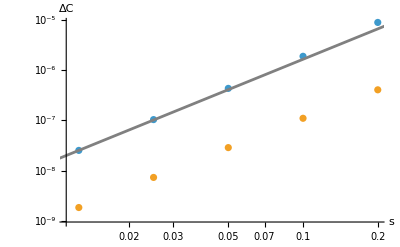

```mathematica
Show[ListLogLogPlot[{Table[{lists[[i]],Abs[modesGenNum[[i]]["Amplitudes"]["ℐ"]-modesGenAna[[i]]["Amplitudes"]["ℐ"]]},{i,1,Length[lists]}],Table[{lists[[i]],Abs[modesGenNum[[i]]["Amplitudes"]["ℋ"]-modesGenAna[[i]]["Amplitudes"]["ℋ"]]},{i,1,Length[lists]}]},AxesLabel->{s,ΔC}],LogLogPlot[(s/0.0125)^2*2.55*^-8,{s,0.001,1},PlotStyle->Gray]]
```

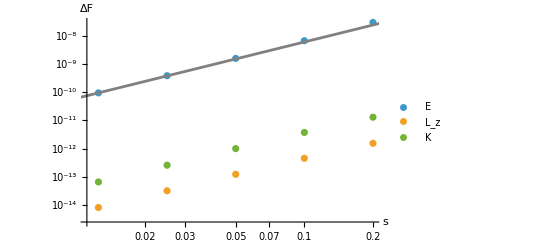

```mathematica
Show[ListLogLogPlot[{Table[{lists[[i]],Abs[modesGenNum[[i]]["Fluxes"]["Energy"]["ℐ"]-modesGenAna[[i]]["Fluxes"]["Energy"]["ℐ"]]},{i,1,Length[lists]}],
Table[{lists[[i]],Abs[modesGenNum[[i]]["Fluxes"]["AngularMomentum"]["ℋ"]-modesGenAna[[i]]["Fluxes"]["AngularMomentum"]["ℋ"]]},{i,1,Length[lists]}],
Table[{lists[[i]],Abs[modesGenNum[[i]]["Fluxes"]["CarterConstantK"]["ℋ"]-modesGenAna[[i]]["Fluxes"]["CarterConstantK"]["ℋ"]]},{i,1,Length[lists]}]},AxesLabel->{s,ΔF},PlotLegends->{"E", "L_z","K"}],LogLogPlot[(s/0.0125)^2*9.49*^-11,{s,0.001,1},PlotStyle->Gray]]
```